```mathematica
If[!NumberQ[makePallette],NotebookEvaluate[NotebookDirectory[]~~"visualVocabDefs.nb"],NotebookEvaluate[NotebookDirectory[]~~"vvClear.nb"]];
```

## The Fourier Transform

```mathematica
credits
```

This notebook is part of A Visual Vocabulary for Image Processing. All rights are reserved by the authors, W. A. Sethares and C. R. Johnson, Jr. Last revised Jan 2017. All x-ray images are used with permission of the Van Gogh Museum and the Rijksmuseum, Amsterdam, The Netherlands. Please do not violate the trust of the museums that have provided access to their x-ray images by distributing this data in any form.

Individual sine waves may have limited artistic and scientific value. However, combinations of sine waves can be used to describe, analyze, and synthesize almost any possible signal, almost any possible sound, almost any possible image. The Fourier transform is the tool of choice when faced with analyzing and understanding the sinusoidal makeup of a signal.

```mathematica
TableForm[{{Hyperlink["Spectrum2Sines",{"visualVocabFourier.nb","labelFFT2SinesA"}],labelFFT2SinesA},{Hyperlink["SpectrumAlternatingModel",{"visualVocabFourier.nb","labelAlternatingFFTA"}],labelAlternatingFFTA},
{Hyperlink["SpectrumDropouts",{"visualVocabFourier.nb","labelFFTDropoutsA"}],labelFFTDropoutsA},
{Hyperlink["Zero-padding",{"visualVocabFourier.nb","labelFFTZeroPadA"}],labelFFTZeroPadA},{Hyperlink["ApproximatingAndInverting",{"visualVocabFourier.nb","labelFFTApproxA"}],labelFFTApproxA},{Hyperlink["2DSinusoids",{"visualVocabFourier.nb","label2DSinesA"}],label2DSinesA},{Hyperlink["2DSinusoidalSpectra",{"visualVocabFourier.nb","labelFFTEggCartonA"}],labelFFTEggCartonA},{Hyperlink["SpectrumCanvasModels",{"visualVocabFourier.nb","labelFFTCanvasA"}],labelFFTCanvasA},{Hyperlink["SpectrumCanvasTopoMap",{"visualVocabFourier.nb","labelFFTTopoMapA"}],labelFFTTopoMapA},{Hyperlink["SpectrumCanvasContour",{"visualVocabFourier.nb","labelFFTContourA"}],labelFFTContourA}}]
```

| The Fourier transform (spectrum) of the sum of two sinusoids shows peaks at each of the two frequencies
 | The spectrum of a signal that has alternately wide and narrow peaks.
 | Spectrum of the alternating model with dropouts
 | Zero-padding can help to improve the accuracy of the estimated frequency
 | Reconstructing a signal from different numbers of coefficients: more coefficients give a closer match
 | The outer product of two 1D sinusoids: an abstract egg flat
 | The 2D spectrum of the egg flat
 | Exploring 2D spectra
 | Exploring 2D spectra visualized as a 3D plot
 | Exploring 2D spectra visualized as a contour plot

The important new commands in this notebook are Fourier[ ] and InverseFourier[ ], which work to calculate the spectrum of both one and two dimensional signals (and the inverse, which calculates the signal from the spectrum).

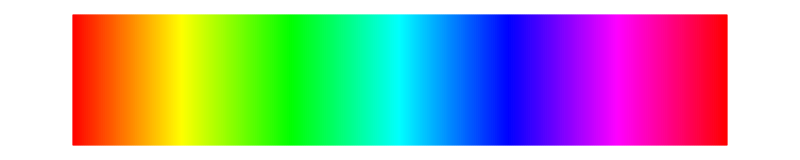

```mathematica
specLine
```

Since signals are waves, they have many properties that are analogous to the wave properties of light. Think of a prism, which bends each color through a different angle and so decomposes sunlight into a family of colored beams. Each beam contains a “pure color,”' a wave of a single frequency, amplitude, and phase. Similarly, complex signals can be decomposed into a family of simple sine waves, each of which is characterized by its frequency, amplitude, and phase. These are called the partials, or the overtones of the signal, and the collection of all the partials is called the spectrum. The figure below depicts the Fourier transform in its role as a “signal” prism. When the signal is a light wave or a sound wave, there are special words that describe the various frequency regions: high frequencies correspond to blue light or treble sound, middle frequencies correspond to yellow light or midrange sound, low frequencies correspond to red light or bass sound. No matter the source of the signal, the decomposition into sinusoids of different frequencies is the same once the signal has been digitized for computer processing.

```mathematica
Column[{Image[-Graphics-, ImageSize -> 547] , 
  Style["Just as a prism separates light into its simple constituent elements (the colors of the rainbow), the Fourier transform separates signals into simpler sine waves in the low, middle, and high frequency ranges.", captionStyle]}, Alignment -> Center](* soundPrism.eps *)
```

-Graphics-
Just as a prism separates light into its simple constituent elements (the colors of the rainbow), the Fourier transform separates signals into simpler sine waves in the low, middle, and high frequency ranges.

### One Dimensional Fourier Transforms

What does the FFT do? In many common applications, the FFT is used to locate the frequencies in a signal. For example, if t is a time variable, the default values in the following example show two sinusoids with frequencies 10.7 and 17.2 Hz, plotted over one second. The amplitude of the second sine is a bit smaller than the amplitude of the first. The spectrum of each sinusoid is shown directly below; observe that the peak in the spectrum of the first occurs at the index 11 and the peak in the second occurs at index 17. Thus the computed spectra show the approximate frequencies of the sinusoids. Moreover, the third plot on the top shows the sum of the two sine waves while the third plot on the bottom shows the spectrum of the sum. Even though the two sine waves are mixed inextricably together in time, the two sinusoids are well separated in frequency. Moreover, the relative amplitudes of the two sinusoids is apparent in the spectrum. This happens in general: the spectrum breaks a signal apart into sinusoidal pieces.

```mathematica
labelFFT2SinesA="The Fourier transform (spectrum) of the sum of two sinusoids shows peaks at each of the two frequencies";
infoFFT2SinesA="The top row shows two sinusoids, one is plotted on the left, the other in the middle, and the sum is plotted on the right. The frequencies of the sinusoids are specified by the two sliders and the third slider controls the amplitude of the second sinusoid.\n\nThe bottom row shows the corresponding Fourier transforms.\n\nThe location of the peaks of the spectra show the frequencies of the sinusoids.\n\nChange the frequencies; observe how the peaks in the spectrum move left and right as a result.\n\nChange the amplitude of the sines; observe how the height of the peaks changes in response.";
Manipulate[GraphicsGrid[{{Plot[Sin[2 Pi f1 t],{t,0,1},PlotRange->{{0,1},{-2,2}},PlotLabel->"first sinusoid"],Plot[a Sin[2 Pi f2 t],{t,0,1},PlotRange->{{0,1},{-2,2}},PlotLabel->"second sinusoid"],Plot[Sin[2 Pi f1 t]+a Sin[2 Pi f2 t],{t,0,1},PlotLabel->"sum of two sinusoids"]},{ListPlot[Abs[Fourier[Table[Sin[2 Pi f1 t],{t,0,1,1/1000}]]][[2;;50]],PlotRange->All,Filling->Axis,PlotLabel->"Fourier transform first sinusoid"],ListPlot[Abs[Fourier[Table[a Sin[2 Pi f2 t],{t,0,1,1/1000}]]][[2;;50]],PlotRange->All,Filling->Axis,PlotLabel->"Fourier transform second sinusoid"],ListPlot[Abs[Fourier[Table[Sin[2 Pi f1 t]+a Sin[2 Pi f2 t],{t,0,1,1/1000}]]][[2;;50]],PlotRange->All,Filling->Axis,PlotLabel->"Fourier transform of sum"]}},ImageSize->700],{{f1,17.2,"frequency of first sinusoid"},1,50,Appearance->"Labeled"},{{f2,10.7,"frequency of second sinusoid"},1,50,Appearance->"Labeled"},Row[{Control[{{a,0.8,"relative amplitude"},0,2,Appearance->"Labeled"}],Spacer[20],info[infoFFT2SinesA]}],FrameLabel->Style[labelFFT2SinesA,Medium],TrackedSymbols->{f1,f2,a},ContinuousAction->False,SaveDefinitions->True]
```

Since the time period is 1 second, the frequency f1 specifies the number of sinusoidal periods over that one second. When f1=17.2, there are exactly 17.2 sinusoidal undulations in the plot (turn the amplitude slider to zero to see it more clearly, or change f1 to an integer to make it easier to count). Similarly for f2, the frequency shown by the FFT describes the number of sinusoidal periods over the time extent of the data.

Let's interpret the features of the above figure from a slightly different perspective. When examining the sum of the two sinusoids, it is not always clear visually (depending on the particular values shown) what the constituent elements are. How does the Fourier transform do it? The inside Fourier transforms notebook shows that the transform is a collection of correlations, one with each possible sinusoidal frequency. The value of the the spectrum at each frequency is the correlation of the signal with the sine wave of that frequency. So for example, in the demonstration above with the default values, sinusoids of frequency 11 and 17 correlate strongly with the sum. All others are smaller (though nearby peaks, such as 10 and 18, may also be fairly large. Observe that when the frequencies are integers, there is little or no leakage to nearby frequency locations). Now recall that when two signals are strongly correlated, they are similar to each other, they “point in the same direction.” Thus a good way to interpret the spectrum is that the largest peaks indicate sinusoids that fit well with the signal.

```mathematica
specLine
```

-Graphics-

What about signals that do not obviously consist of sums of sinusoids? The following example generates a signal that mimics some of the features of a thread canvas, as discussed in the alternating model, and calculates the spectrum.

```mathematica
labelAlternatingFFTA="The spectrum of a signal that has alternately wide and narrow peaks.";
infoAlternatingFFTA="The alternating model has several degrees of freedom: \n\nParameters a and b control the widths of the two (alternating) peaks.\nThe amp parameter controls the relative size of the peaks.\nThe noise parameter adds noise.\nThe slope parameter adds a trend.\n\nThe right hand figure shows the spectrum of the model. Observe that with the default parameters, there are 10 complete cycles (each cycle being a pair of one-narrow-one-wide peaks). The largest peak of the spectrum is precisely at 10. \n\nObserve that this answer is robust to changes in the slope, to additions of noise, and to changes in the relative amplitude even for large changes. \n\nAs the widths of the peaks change, the spectral peaks move: increasing the width of a (or of b, or both) decreases the frequency of the main spectral peak. \n\nDecreasing the widths of the a (or b) increases the frequency of the main spectral peaks. \n\nThere are often many harmonics, occurring at integer multiples of the fundamental.\n\nPlay the animations. When changing a or b, the peaks of the spectrum move all around (as expected). When changing the amplitude, the peaks remain reasonably fixed, except for extreme values of the amplitude. When changing the noise or slope, the peaks tend to remain fixed.";
altFun[x_,a_,b_,amp_]:=Piecewise[{{altFun[x-(a+b),a,b,amp],x>a+b},{Sin[2 Pi/a x],0<x<a},{amp Sin[2 Pi/b (x-a)],a<x<a+b},{altFun[x+(a+b),a,b,amp],x<0}}];
Manipulate[altSamp=Table[slope (x-1/2)+0.5 Clip[altFun[x,a,b,amp],{0,1.2}]+RandomVariate[NormalDistribution[0.3,σ]],{x,0,1,1/500}];
GraphicsRow[{ListLinePlot[altSamp,PlotRange->{0,1},ImageSize->300,PlotLabel->"The Alternating Model"],ListPlot[Abs[Fourier[altSamp]][[2;;50]],PlotRange->All,Filling->Axis,ImageSize->300,PlotLabel->"Fourier Transform"]}],Row[{Control[{{a,0.02},0,0.2,Appearance->"Labeled"}],Spacer[20],Control[{{b,0.08},0,0.2,Appearance->"Labeled"}]}],Row[{Control[{{amp,1},0,1.2}],Spacer[20],Control[{{slope,0,"slope"},-0.4,0.4}]}],Row[{Control[{{σ,0.001,"noise"},0.001,0.16}],Spacer[50],info[infoAlternatingFFTA]}],FrameLabel->Style[labelAlternatingFFTA,Medium],TrackedSymbols->{a,b,amp,σ,slope},SaveDefinitions->True]
```

Observe that the Fourier transform shows the basic periodicity of the signal, and this may or may not correspond to the number of peaks in the signal. For example, at the default values a=0.02, b=0.08, the basic period is 10 (there is one narrow-wide in each cycle). As the values move closer together (say by a=0.05 and b=0.08) the main period near 16, which can be observed by counting the peaks. The general shape of the spectrum and even the location of the major spectral peaks are resilient to changes in the parameters: when there is a significant amount of noise, the largest peak remains at the same location. If the trend is nonzero, only the lowest frequency terms change and the peak still remains at the desired value 10 (using the default parameters). Thus the FFT method is reasonably resilient (at least for models of these classes) to changes in the amplitude, noise, and slope.

```mathematica
specLine
```

-Graphics-

Another common imperfection in signals is that the data may be missing at some points or the signal may flatten out for a portion of its length. With the Fourier transform, for small dropouts, there is little change in the spectrum.

```mathematica
labelFFTDropoutsA="Spectrum of the alternating model with dropouts";
infoFFTDropoutsA="The Fourier transform is quite robust to dropouts. \n\nWith all the same parameters as the alternating model, this adds two sliders that define a start and an end point where the signal disappears. \n\nThe spectrum of the signal is shown on the right. \n\nInterestingly, small dropouts have little impact, while even large dropouts leave the major features of the spectrum intact.";
Manipulate[altSamp=Table[slope (x-1/2)+0.5 Clip[altFun[x,a,b,amp],{0,1.2}]+RandomVariate[NormalDistribution[0.3,σ]],{x,0,1,1/500}];
lineDrop=Flatten[{altSamp[[1;;Round[Min[st,en]]]],ConstantArray[Mean[altSamp],Max[Round[en-st],1]],altSamp[[Round[en];;Length[altSamp]]]}];
GraphicsRow[{ListLinePlot[lineDrop,PlotRange->{0,1},ImageSize->300,PlotLabel->"The Alternating Model with Dropouts"],ListPlot[Abs[Fourier[lineDrop]][[2;;50]],PlotRange->All,Filling->Axis,ImageSize->300,PlotLabel->"Fourier Transform"]}],Row[{Control[{{a,0.02},0,0.2,Appearance->"Labeled"}],Spacer[20],Control[{{b,0.08},0,0.2,Appearance->"Labeled"}]}],Row[{Control[{{amp,1},0,1.2}],,Spacer[20],Control[{{slope,0,"slope"},-0.4,0.4}]}],{{σ,0.001,"noise"},0.001,0.16},Row[{Control[{{st,100,"start dropout"},1,Dynamic[Length[lineDrop]],1}],Spacer[20],Control[{{en,200,"end dropout"},1,Dynamic[Length[lineDrop]],1}],Spacer[20],info[infoFFTDropoutsA]}],FrameLabel->Style[labelFFTDropoutsA,Medium],TrackedSymbols->{a,b,amp,σ,slope,en,st},SaveDefinitions->saveDef]
```

HW: Can you make the peak move from one location to another by changing the drop-out width? How wide (as a percentage of the total length) does the drop-out need to be?

```mathematica
specLine
```

-Graphics-

One quirk of the Fourier method is that it inherently returns an integer answer for the frequency even though there is no reason to expect that any given signal will have an integer number of periods within the analysis region. This limitation can be overcome (somewhat) by zero-padding: add a large number of zero elements to the end of the signal and then calculate a larger FFT. For example, doubling the length of the FFT causes the answer to have twice the resolution. In reality, this is a kind of interpolation in the frequency domain where it is easier to judge what the underlying frequencies are. The next example takes its input from a single row of an image, as was done here. The image in the upper left is used to choose a row from the image and this row is plotted as a function in the upper right. The Fourier transform of this row is shown in the lower left. The slider called zero-padding factor concatenates zeros onto the row (when the slider is 2, the length is doubled, when 3, the length is tripled, etc.). The bottom right shows the Fourier transform of the zero-padded signal. Observe that this tends to show the same peaks as the unpadded spectrum, but it has more points and hence gives a better estimate of the frequency of the signal.

```mathematica
labelFFTZeroPadA="Zero-padding can help to improve the accuracy of the estimated frequency";
infoFFTZeroPadA="Zero-padding pads a signal with a large number of zeroes and calculates a larger FFT. This is a kind of frequency domain interpolation, and may make it easier to locate the underlying frequency of the signal. \n\nA particular row (upper right) is chosen from the image (upper left). The spectrum of the row is on the bottom left and of the zero-padded row is in the bottom right. \n\nIt is almost always easier to see the true location of the peak in the zero-padded spectrum.";
Manipulate[{col,row}=ImageDimensions[allIm[[i]]];
tLine=threadLine[allIm[[i]],row-thisRow+1];
zeroPadThreadLine=PadRight[tLine,n Length[tLine]];
fftZeroPadLine=Abs[Fourier[zeroPadThreadLine]][[n+1;;50 n]];
freqAxis=(Range[49n]+n-1)/n;
rowNum=thisRow;
fftLine=Abs[Fourier[tLine]][[2;;50]];
GraphicsGrid[{{Show[Image[allIm[[i]],ImageSize->250],Graphics[{Green,Opacity[0.4],Thickness[0.02],Line[{{0,thisRow},{col,thisRow}}]}]],ListLinePlot[tLine,PlotRange->{{1,col},{0,1}},ImageSize->250,PlotLabel->"Row "~~ToString[rowNum]]},{ListPlot[fftLine,PlotRange->All,Filling->Axis,ImageSize->250,PlotLabel->"Fourier Transform of row "~~ToString[rowNum]],ListPlot[Transpose[{freqAxis,fftZeroPadLine}],PlotRange->All,Filling->Axis,ImageSize->250,PlotLabel->"Fourier Transform of row "~~ToString[rowNum]~~" upsampled by "~~ToString[n]]}}],Row[{Control[{{i,2,"image"},Thread[Range[Length[allIm]]->allImNames],ControlType->PopupMenu}],Spacer[20],Control[{{thisRow,383,"row"},1,row-1,1,Appearance->"Labeled"}]}],
Row[{Control[{{n,2,"zero-pad factor"},2,10,1,Appearance->"Labeled"}],Spacer[20],info[infoFFTZeroPadA]}],{row,400,ControlType->None},FrameLabel->Style[labelFFTZeroPadA,Medium],TrackedSymbols->{thisRow,n,i},SaveDefinitions->saveDef]
```

HW: How much zero-padding is needed to make the peak have a width of 5 bins? 10 bins? At what value does it cease to help give a better estimate of the frequency of the signal?

HW: Implement a method of estimating the frequency of the 2D rectangle-model using (two-dimensional) parabolic interpolation.

```mathematica
specLine
```

-Graphics-

The Fourier spectrum is not only adept at analyzing signals but also at reconstructing and approximating signals. The following demonstration decomposes and then rebuilds a wave using the Fourier transform and its inverse. Select one of the waveforms from the chooser box. The waveform is displayed in blue on the right and the spectrum is shown on the left. The slider controls how many terms are used in the reconstructed signal (the reconstruction is shown on the right in brown). The shaded area is the difference between the blue original and the brown reconstruction. Placing the slider all the way to the right uses all 100 terms and the reconstruction is exact. As fewer terms are used, the error in the reconstruction grows larger. Waveshapes which are close to sinusoidal only need a few terms to squeeze the blue area; waves which are impulsive or have complex shapes have larger reconstruction errors.

```mathematica
labelFFTApproxA="Reconstructing a signal from different numbers of coefficients: more coefficients give a closer match";
infoFFTApproxA="This demonstration decomposes and then rebuilds signals using the DFT and the inverse DFT.\n\nChoose a waveform from the selection box. It is displayed in blue on the right.\n\nThe left hand plot shows the spectral decomposition (i.e., the magnitude of the DFT) of the signal.\n\nThe slider controls how many terms are used to reconstruct the signal, which is shown on the right in brown.\n\nThe shaded area is the difference between the blue original and the brown reconstruction.\n\nPlacing the slider all the way to the right uses all 100 terms and the reconstruction is exact. With fewer terms, the error is larger.\n\nSignals which are close to sinusoidal only need a few terms to squeeze the blue area; waves which are impulsive or have complex shapes tend to have larger reconstruction errors.\n\nThe small black dots show which terms in the DFT are being used in the reconstruction (with one term, only the largest value is used, with two terms, only the two largest, etc.)\n\nAnimate the 'number of terms' slider and observe how quickly (or not) the approximations converge to the signal.";
Manipulate[Module[{sig,lenSig,fftY,mag,phase,ordMag,rec},
sig=allSigs[[thisSig]];lenSig=Length[sig];
fftY=Fourier[sig,FourierParameters->{1,-1}];
mag=Abs[fftY]/lenSig;phase=Arg[fftY];
ordMag=Ordering[mag,All,GreaterEqual];
rec=Total[Table[mag[[ordMag[[k]]]] Cos[2 Pi (ordMag[[k]]-1) (n-1)/lenSig+phase[[ordMag[[k]]]]],{k,1,numTerms},{n,1,lenSig}]];
GraphicsRow[{ListPlot[{Tooltip[mag,"not used"],Tooltip[Thread[{ordMag[[1;;numTerms]],mag[[ordMag[[1;;numTerms]]]]}],"used in reconstruction"]},Filling->Axis,PlotRange->All,PlotLabel->"Fourier Transform of Signal",PlotStyle->{Blue,{Black,PointSize[0.015]}}],ListLinePlot[{Tooltip[sig,"signal"],Tooltip[rec,"reconstruction"]},PlotLabel->"Signal (blue) and Reconstructed Signal (brown)",PlotRange->All,Filling->{1->{2}}]},ImageSize->800]],
Row[{Control[{{thisSig,4,""},Thread[Range[numSigs]->sigNames],ControlType->SetterBar}],Spacer[20],info[infoFFTApproxA]}],{{numTerms,5,"number of terms in reconstruction"},1,100,1,Appearance->"Labeled"},
FrameLabel->Style[labelFFTApproxA,Medium],TrackedSymbols->{numTerms,thisSig},SaveDefinitions->saveDef]
```

Since the Fourier transform is invertible, the transform neither creates nor destroys information. The inversion is most simply applied in Mathematica using InverseFourier[ ]. The combination of the transform and its inverse can be used to implement any linear filter. The procedure is: (1) take the DFT of the signal (2) modify the spectrum  X[n] (for instance, by setting some terms to zero or weighting some of the terms) (3) take the inverse. The resulting output is the filtered signal. In the demonstration above, the brown reconstructed signal is a filtered version of the original blue signal. Perhaps an even more important use of the transform is in the design of linear filters, as dicussed in the filter design notebook.

### Two Dimensional Fourier Transforms

Fourier transforms work much the same in two dimensions as in one. To gain some intuition about two dimensional transforms, remember that Fourier Transforms are ideal for locating sinusoids. The 2D FFT is no exception; it looks for 2D sinusoids! Here are some 2D sinusoids: change the frequency in the vertical direction and the frequency in the horizontal direction, and for fun, add some noise.

```mathematica
label2DSinesA="The outer product of two 1D sinusoids: an abstract egg flat";
info2DSinesA="2D sinusoids have two frequency terms, one in the vertical and one in the horizontal directions. \n\nWith the default values of 3 and 5, there are 3 undulations in the vertical direction and 5 in the horizontal direction. \n\nIncrease the frequencies and observe the extra white rectangles appear. \n\nAdd noise and the surface becomes textured.";
Manipulate[Module[{r,s,x},r=Table[Sin[2 Pi f1 t],{t,0,1,1/199}];
s=Table[Sin[2 Pi f2 t],{t,0,1,1/199}];
x=Outer[Times,r,s]+n RandomReal[{-1,1},{200,200}];
GraphicsRow[{Image[x,ImageSize->{300,300}],ListPlot3D[x,Mesh->None,ColorFunction->"CoffeeTones",ImageSize->{300,300}]}]],{{f1,3,"vertical frequency"},1,20,Appearance->"Labeled"},{{f2,5,"horizontal frequency"},1,20,Appearance->"Labeled"},
Row[{Control[{{n,0.001,"noise"},0.001,5}],Spacer[20],info[info2DSinesA]}],
FrameLabel->Style[label2DSinesA,Medium],TrackedSymbols->{f1, f2, n},SaveDefinitions->saveDef]
```

```mathematica
specLine
```

-Graphics-

What does the spectrum of this egg-flat look like?

```mathematica
labelFFTEggCartonA="The 2D spectrum of the egg flat";
infoFFTEggCartonA="2D sinusoids operate as in the previous interactive example. \n\nThe spectrum (the 2D Fast Fourier Transform or FFT) is shown on the right. \n\nFor the default frequency values (3 and 5) the spectrum consists of 4 peaks (the four dark spots on the right). \n\nCount how far it is from the center point (zero frequency) to each peak. (Using the zoom slider may help). The answer is that the upper right spot is 5 over and 3 up. \n\nThis is no coincidence: the peaks always occur at the largest frequencies, just like in 1D. \n\nAdd noise. Even with a lot of noise (turn the slider all the way to the right) the four peaks remian prominent. \n\nChange the frequencies: observe the relationship between the new frequency and the location of the peak.";
Manipulate[Module[{r,s,x,xf,xCentered,d1,d2},
r=Table[Sin[2 Pi f1 t],{t,0,1,1/199}];
s=Table[Sin[2 Pi f2 t],{t,0,1,1/199}];
x=Outer[Times,r,s]+n RandomReal[{-1,1},{200,200}];
xf=Abs[Fourier[x,FourierParameters->{1,-1}]];
{d1,d2}=Ceiling[Dimensions[xf]/2];
xCentered=RotateLeft[xf,{d1,d2}];
Row[{Image[x,ImageSize->{300,300}],Spacer[20],ArrayPlot[xCentered,PlotRange->{{d1-zoom+1,d1+zoom+1},{d2-zoom+1,d2+zoom+1}},Frame->True,FrameLabel->{"column of FFT matrix","row of FFT matrix"},FrameTicks->{{{d1+1,Round[d1+1-f1],Round[d1+1+f1]},None},{{d2+1,Round[d2+1-f2],Round[d2+1+f2]},None}},Mesh->True,MeshStyle->Opacity[0.2],ImageSize->{300,300},PlotLabel->"Fourier Transform of Image"]}]],
{{f1,3,"vertical frequency"},1,20,Appearance->"Labeled"},
{{f2,5,"horizontal frequency"},1,20,Appearance->"Labeled"},
{{n,0.001,"noise"},0.001,5},Row[{Control[{{zoom,20},50,3,-1}],Spacer[20],info[infoFFTEggCartonA]}],
FrameLabel->Style[labelFFTEggCartonA,Medium],TrackedSymbols->{f1,f2,n,zoom},SaveDefinitions->saveDef]
```

HW: Look at the spectrum when the horizontal function is defined by Sin^n[ ] rather than Sin[ ]. Explain what you see.

HW: Look at the spectrum when the horizontal function and vertical functions are defined by Sin^n[ ] and Sin^m[ ]. Explain what you see.

HW: Modify the method to display the Log[ ] of the Abs[Fourier[ ]]. How do the peaks corresponding to the sine waves look different. How does the added noise look different?

HW: Rotate the sinusoidal image through an angle θ degrees. Describe the change(s) in the Fourier transform in terms of the angle θ.

```mathematica
specLine
```

-Graphics-

```mathematica
labelFFTCanvasA="Exploring 2D spectra";
infoFFTCanvasA="The spectra of various images and tiles.\n\nThe average frequency in the horizontal direction is given by the distance of the blobs on the left and right along the horizontal axis.\n\nThe spacing of the features in the horizontal direction is inversely proportional to the frequency given by the peaks in the horizontal direction.\n\nThe default image has large values on (or near) the axes and at the four corners.\n\nThere appear to be 'overtones' (harmonically related maxima) in both spatial directions: these may be due to saturation (clipping) in the image, or perhaps to some other nonlinearity that is present.";
Manipulate[Module[{im,xf,xCentered1,img,d1,d2},
im=ImageData[img=allIm[[i]]];
xf=Abs[Fourier[im-Mean[im],FourierParameters->{1,-1}]];
{d1,d2}=Ceiling[Dimensions[xf]/2];
xCentered1=RotateLeft[xf,{d1,d2}];Row[{Image[img,ImageSize->300],ArrayPlot[xCentered1,PlotRange->{{d1-zoom,d1+zoom}+offset[[2]],{d2-zoom,d2+zoom}-offset[[1]]},Frame->True,FrameLabel->{"rows of FFT matrix","columns of FFT matrix"},FrameTicks->{{d1,None},{d2,None}},Mesh->mesh,MeshStyle->Opacity[0.1],ImageSize->{400,400},PlotLabel->"Fourier transform (spectrum) of image"]}]],Row[{Control[{{i,2,"image"},Thread[Range[3]->allImNames[[1;;3]]],ControlType->PopupMenu}],Spacer[20],Control[{{zoom,40},100,3,-1}],Spacer[20],Control[{mesh,{False,True}}],Spacer[20],Control[{{offset,{0,0}},{-38,-38},{38,38}}],Spacer[20],info[infoFFTCanvasA]}],TrackedSymbols->{zoom,mesh,offset,i},SaveDefinitions->saveDef,FrameLabel->Style[labelFFTCanvasA,Medium]]
```

```mathematica
specLine
```

-Graphics-

For example, here’s another way of visualizing the same spectrum that plots height proportional to value (rather than grayscale as above). Grab the 3D image to rotate and look at it from different angles.

```mathematica
labelFFTTopoMapA="Exploring 2D spectra visualized as a 3D plot";
infoFFTTopoMapA="An alternative view of the same spectral information. Instead of plotting the spectrum as an image (where dark and light correspond to large and small) it is plotted as a topographic map, where large values 'stick up' out of the plane and are colored differently. \n\nChange the color scheme. \n\nGrab the 3D representation with the mouse and rotate it to see the surface from other angles. \n\nThe two zoom sliders enlarge either the domain (the x-y axes) or the range (the z axis).";
Manipulate[Module[{im,img,xf,d1,d2,xCentered2},
im=ImageData[img=allIm[[i]]];
xf=Abs[Fourier[im-Mean[im],FourierParameters->{1,-1}]];
{d1,d2}=Ceiling[Dimensions[xf]/2];
xCentered2=RotateLeft[xf,{d1,d2}];
max=Max[xf];
Row[{Image[img,ImageSize->300],ListPlot3D[xCentered2[[d1-zoomD;;d1+zoomD,d2-zoomD;;d2+zoomD]],PlotRange->{0,zoomR},Mesh->None,ColorFunction->colorScheme,ImageSize->{400,400},PlotLabel->"Fourier transform of image"]}]],
Row[{Control[{{i,2,"image"},Thread[Range[3]->allImNames[[1;;3]]],ControlType->PopupMenu}],Spacer[20],Control[{{colorScheme,"ThermometerColors","color scheme"},ColorData["Gradients"]}],Spacer[20],info[infoFFTTopoMapA]}],Row[{Control[{{zoomD,40,"zoom in domain"},100,3,-1}],Spacer[20],Control[{{zoomR,max/2,"zoom in range"},max,max/10}]}],TrackedSymbols->{zoomD,zoomR,i,colorScheme},SaveDefinitions->saveDef,FrameLabel->Style[labelFFTTopoMapA,Medium]]
```

```mathematica
specLine
```

-Graphics-

And here is yet another way of visualizing the same spectrum as a contour plot rather than a grayscale image.

```mathematica
labelFFTContourA="Exploring 2D spectra visualized as a contour plot";
infoFFTContourA="An alternative view of the same spectral information. Instead of plotting the spectrum as an image (where dark and light correspond to large and small) it is plotted as a contour map, where large values are colored differently than small values, and contours (lines of constant value) are drawn to show where changes occur. \n\nChange the color scheme. \n\nThe two zoom sliders enlarge either the domain (the x-y axes) or the range (the z axis).\n\nThe contour slider changes the number of contour lines drawn, increase for a more detailed view.";
Manipulate[Module[{im,img,xf,d1,d2,xCentered3},
im=ImageData[img=allIm[[i]]];
xf=Abs[Fourier[im-Mean[im],FourierParameters->{1,-1}]];
{d1,d2}=Ceiling[Dimensions[xf]/2];
xCentered3=RotateLeft[xf,{d1,d2}];
max=Max[xf];
Row[{Image[img,ImageSize->300],ListContourPlot[xCentered3[[d1-zoomD;;d1+zoomD,d2-zoomD;;d2+zoomD]],PlotRange->{0,zoomR},Contours->contours,ColorFunction->colorScheme,ImageSize->{400,400},PlotLabel->"Fourier transform of image",Frame->False]}]],Row[{Control[{{i,2,"image"},Thread[Range[3]->allImNames[[1;;3]]],ControlType->PopupMenu}],Spacer[20],Control[{{colorScheme,"ThermometerColors","color scheme"},ColorData["Gradients"]}],Spacer[20],Control[{{contours,10},5,50,1}],Spacer[20],info[infoFFTContourA]}],Row[{Control[{{zoomD,40,"zoom in domain"},100,3,-1}],Spacer[20],Control[{{zoomR,max/2,"zoom in range"},max,max/10}]}],TrackedSymbols->{zoomD,zoomR,i,colorScheme,contours},SaveDefinitions->saveDef,FrameLabel->Style[labelFFTContourA,Medium]]
```

Any of these displays may be useful, but remember that they all show the same information; it really is just the mechanism of the display that is different.

HW: Replace the x-ray image with the negative (instead of the x-ray positive). How does the resulting spectrum differ?

HW: Replace the test image with the same rotated image rotated. How does the resulting spectrum differ?

HW: As in 1-D, it is possible to implement zero padding in the spatial domain to help increase the resolution of the signal in the frequency domain. Implement a n-times zero padding for images and compare the output of the method on sinusoidal images and on a thread image.